# Mediator Model Analysis

Isaac R. Wang

This code analysis the freeze-in and out for the mediator model.

## Prepare

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

```mathematica
MakeBoxes[p1,TraditionalForm]:="p_1";
MakeBoxes[p2,TraditionalForm]:="p_2";
MakeBoxes[p3,TraditionalForm]:="p_3";
MakeBoxes[p4,TraditionalForm]:="p_4";
MakeBoxes[mχ,TraditionalForm]:="m_χ";
MakeBoxes[mν,TraditionalForm]:="m_ν";
MakeBoxes[mϕ,TraditionalForm]:="m_ϕ";
MakeBoxes[m1,TraditionalForm]:="m_1";
MakeBoxes[m2,TraditionalForm]:="m_2";
MakeBoxes[yχ,TraditionalForm]:="y_χ";
MakeBoxes[yν,TraditionalForm]:="y_ν";
MakeBoxes[αχ,TraditionalForm]:="α_χ";
MakeBoxes[αν,TraditionalForm]:="α_ν";
MakeBoxes[gH,TraditionalForm]:="g_H";
MakeBoxes[mpl,TraditionalForm]:="m_pl";
MakeBoxes[E1,TraditionalForm]:="E_1";
MakeBoxes[vsq,TraditionalForm]:="v^2";
MakeBoxes[Γϕ,TraditionalForm]:="Γ_ϕ";
MakeBoxes[Y∞,TraditionalForm]:="Y_∞";
MakeBoxes[Yf,TraditionalForm]:="Y_f";
MakeBoxes[xf,TraditionalForm]:="x_f";
MakeBoxes[Nν,TraditionalForm]:="N_ν";
MakeBoxes[Nχ,TraditionalForm]:="N_χ";
$Assumptions={{2mχ-mϕ,s-4 mχ^2,mχ,mϕ,T,s,y,gH,mpl,x,v,2-v}>0};
GeV=10^3;(*Unit MeV*)
```

## Scattering amplitude and cross section

The Lagrangian of the model is

L=y_χ χ̄ ϕ_μ γ^μ P_L χ+y_ν ν̄ ϕ_μ γ^μ P_L ν
L=y_χ ν χ ϕ

The scattering amplitude can be computed in the following way.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,m1,m1,m2,m2];
M=yχ yν(SpinorVBar[p2,m1].GA[μ].GA[7].SpinorU[p1,m1])MT[μ,ν]/(SP[p1+p2,p1+p2]-mϕ^2)(SpinorUBar[p3,m2].GA[ν].GA[7].SpinorV[p4,m2])//Contract;
Msq=FermionSpinSum[ComplexConjugate[M]*M,ExtraFactor->1/4]//DiracSimplify//Simplify
```

(y_ν^2 y_χ^2 (m_1^2+m_2^2-u)^2)/((m_ϕ^2-s)^2)

The 2 couplings are always connected with each other here. So this time we just assume they are the same.
One feature of this amplitude is that we are using general m_1 and m_2. In specific status, we should pick which one is which.

```mathematica
pf=(√s)/2;
pi=√(s/4-mχ^2);
Msqχtoν=Msq/.{m1->mχ,m2->0,yν->y,yχ->y,u->mχ^2-2(s/4+pi pf cosθ)};
σχν[mχ_,mϕ_,y_,s_]=1/(32π s)pf/pi Integrate[Msqχtoν,{cosθ,-1,1}]//Simplify
```

(y^4 (s-m_χ^2))/(48 π √(1-(4 m_χ^2)/s) (m_ϕ^2-s)^2)

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,0,0,m2,m2];
M=yχ^2(SpinorVBar[p3,m2].GA[7].SpinorU[p1,0])1/(t-mϕ^2)(SpinorUBar[p4,m2].GA[7].SpinorV[p2,0])//Contract;
Msq=FermionSpinSum[ComplexConjugate[M]*M,ExtraFactor->1/4]//DiracSimplify//Simplify
pf=(√s)/2;
pi=√(s/4-mχ^2);
Msqχtoν=Msq/.{m2->mχ,yν->y,yχ->y,t->mχ^2-2(s/4-pi pf cosθ)};
σχνt[mχ_,mϕ_,y_,s_]=1/(32π s)pf/pi Integrate[Msqχtoν,{cosθ,-1,1}]//Simplify
σνχt[mχ_,mϕ_,y_,s_]=1/(32π s)pi/pf Integrate[Msqχtoν,{cosθ,-1,1}]//Simplify
```

(y_χ^4 (m_2^2-t)^2)/(4 (m_ϕ^2-t)^2)

(y^4 ((2 s m_ϕ^2+4 (m_ϕ^2-m_χ^2)^2)/(s m_ϕ^2+(m_ϕ^2-m_χ^2)^2)+(8 (m_χ-m_ϕ) (m_χ+m_ϕ) coth^-1((s-2 m_χ^2+2 m_ϕ^2)/(√(s (s-4 m_χ^2)))))/(√(s (s-4 m_χ^2)))))/(128 π √s √(s-4 m_χ^2))

(y^4 √(s-4 m_χ^2) ((2 s m_ϕ^2+4 (m_ϕ^2-m_χ^2)^2)/(s m_ϕ^2+(m_ϕ^2-m_χ^2)^2)+(8 (m_χ-m_ϕ) (m_χ+m_ϕ) coth^-1((s-2 m_χ^2+2 m_ϕ^2)/(√(s (s-4 m_χ^2)))))/(√(s (s-4 m_χ^2)))))/(128 π s^(3/2))

```mathematica
σνχt[mχ,mϕ,y,s]//TrigToExp//Simplify
```

(y^4 √(s-4 m_χ^2) ((2 s m_ϕ^2+4 (m_ϕ^2-m_χ^2)^2)/(s m_ϕ^2+(m_ϕ^2-m_χ^2)^2)+(4 (m_χ-m_ϕ) (m_χ+m_ϕ) (log((√(s (s-4 m_χ^2)))/(s-2 m_χ^2+2 m_ϕ^2)+1)-log(1-(√(s (s-4 m_χ^2)))/(s-2 m_χ^2+2 m_ϕ^2))))/(√(s (s-4 m_χ^2)))))/(128 π s^(3/2))

Large x, low T, large m

```mathematica
1/(8 mχ^4 T BesselK[2,mχ/T]^2)Integrate[σνχt[mχ,mχ,y,s] √s(s)*BesselK[1,(√s)/T]//Simplify,{s,4 mχ^2,∞}]/.{T->mχ/x}
```

(y^4 (1x)^2)/(128 π m_χ^2 (2x)^2)

```mathematica
1/(8 mχ^4 T BesselK[2,mχ/T]^2)/.{T->mχ/x}
```

x/(8 m_χ^5 (2x)^2)

```mathematica
σχνt‵highT=1/(8 mχ^4 T BesselK[2,mχ/T]^2)Integrate[(σχνt[mχ,0,y,s])BesselK[1,(√s)/T],{s,4 mχ^2,∞}]/.{T->mχ/x}
```

$Aborted

## Thermal averaged cross section

The computed thermal averaged cross section should be in the comoving frame in the early universe. The final result should be found in Gondolo and Gelmini, eq 3.8, i.e.

⟨σ v_Mol⟩=1/(8 m_χ^4 T (K_2(m_χ/T))^2)∫_(4 m_χ^2)^∞ σ √s(s-4 m_χ^2) K_1((√s)/T)ⅆs

Here the  is the Moller velocity, different from the relative velocity in the CM frame.

On the other hand, we can also work in the CM frame and translate it back. Whether or not we use CM frame is completely arbitrary and we can pick the most convenient one. Replace  with , we have

```mathematica
ssol=Solve[(√(s/4-mχ^2)4/(√s)//Simplify)==v,s][[1]]//Normal
σvcm[mχ_,mϕ_,y_,v_]=σχν[mχ,mϕ,y,s]*√(s/4-mχ^2)4/(√s)/.ssol//Simplify
σvcmser[mχ_,mϕ_,y_,v_]=Series[σvcm[mχ,mϕ,y,v],{v,0,2}]//Normal
{a,b}=CoefficientList[σvcmser[mχ,mϕ,y,v],{v}][[{1,3}]]//Simplify
```

{s→-(16 m_χ^2)/(v^2-4)}

-(m_χ^2 (v^2-4) (v^2+12) y^4)/(24 π (16 m_χ^2+m_ϕ^2 (v^2-4))^2)

(2 m_χ^2 y^4)/(π (16 m_χ^2-4 m_ϕ^2)^2)-(m_χ^2 v^2 y^4 (2 m_χ^2+m_ϕ^2))/(24 π (4 m_χ^2-m_ϕ^2)^3)

{(m_χ^2 y^4)/(8 π (m_ϕ^2-4 m_χ^2)^2),(m_χ^2 y^4 (2 m_χ^2+m_ϕ^2))/(24 π (m_ϕ^2-4 m_χ^2)^3)}

Note: the coefficient for the 0-th order is nothing but the s-wave annihilation cross section, i.e. .
Notice that  always appears in , so we can always take the series expansion whether we have relativistic case.

The thermal average gives , thus we have

```mathematica
σv0[mχ_,mϕ_,y_]=a
σvcmavg[mχ_,mϕ_,y_,x_]=a+6b/x
```

(m_χ^2 y^4)/(8 π (m_ϕ^2-4 m_χ^2)^2)

(m_χ^2 y^4 (2 m_χ^2+m_ϕ^2))/(4 π x (m_ϕ^2-4 m_χ^2)^3)+(m_χ^2 y^4)/(8 π (m_ϕ^2-4 m_χ^2)^2)

Actually, this computation is not 100% correct. For large , this is OK. However for small , we can see this diverges, and it should not happen (at  of course this should not diverge). The problem comes from the thermal average. The  comes from integration range for  from 0 to ∞, however it should be from 0 to 2. This approximation is good only when  is large so that the extra contribution from large  disappears. To check the correct behavior, we should have

```mathematica
σavg=Integrate[4π v^2 Exp[-x v^2/4]σvcmser[mχ,mϕ,y,v],{v,0,2}]/Integrate[4π v^2 Exp[-x v^2/4],{v,0,2}]//Simplify;
Limit[σavg,x->0]
Limit[σavg,x->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(3 m_χ^2 y^4 (4 m_χ^2-3 m_ϕ^2))/(40 π (m_ϕ^2-4 m_χ^2)^3)

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(m_χ^2 y^4)/(8 π (m_ϕ^2-4 m_χ^2)^2)

Note: the large , low  limit in the CM frame is complicated! That’s why we always use this form only in the large  case.

This is computed in the CM frame. According to Gondolo and Gelmini, 1991, eq 3.18, translation factor from CM to comoving frame is

```mathematica
Limit[1/2(1+BesselK[1,x]^2/BesselK[2,x]^2),{x->0}]
Limit[1/2(1+BesselK[1,x]^2/BesselK[2,x]^2),{x->∞}]
Series[1/2(1+BesselK[1,x]^2/BesselK[2,x]^2),{x,0,2}]//Normal
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

x^2/8+1/2

In the large x limit, indeed this goes to the CM result.

To make approximation, we take large and small  limit. 
- For low , large , we can directly use the CM result.
- For high , low , it is much easier to directly work with the original formula from Gondolo and Gelmini, eq 3.8.

```mathematica
σvmol‵highT=1/(8 mχ^4 T BesselK[2,mχ/T]^2)Integrate[σχν[mχ,0,y,s] s/(s-mχ^2)√s(s-4 mχ^2)*BesselK[1,(√s)/T],{s,4 mχ^2,∞}]/.{T->mχ/x}(*Large T, ignore mϕ^2 and mχ^2 but cannot ignore 4mχ^2.*)
```

(y^4 (1x)^2)/(96 π m_χ^2 (2x)^2)

OK now we have the asymptotic behavior for both large and small . The good approximation form can be taken as

⟨σ v⟩=(⟨σ v⟩_0)/(1+T/Λ)^2

where the nominator is the s-wave behavior.

Use the approximation form and match coefficients, we have

```mathematica
σvapp[mχ_,mϕ_,y_,Λ_,T_]=σv0[mχ,mϕ,y]/(1+T/Λ)^2;
l1=Series[σvapp[mχ,mϕ,y,Λ,mχ/x],{x,0,2}]//Normal
l2=Series[σvmol‵highT,{x,0,2}]//Normal
match=Solve[l1==l2,Λ][[-1]]
σv[mχ_,mϕ_,y_,T_]=σvapp[mχ,mϕ,y,Λ,T]/.match//Simplify
```

(Λ^2 x^2 y^4)/(8 π (m_ϕ^2-4 m_χ^2)^2)

(x^2 y^4)/(384 π m_χ^2)

{Λ→(4 m_χ^2-m_ϕ^2)/(4 √3 m_χ)}

(m_χ^2 y^4)/(8 π (m_ϕ^2-4 m_χ (m_χ+√3 T))^2)

Note here we use the fact that we consider  to avoid off-shell  decay into .

## Boltzmann equation

The Boltzmann equation can always be written as

(ⅆ(n a^3))/ⅆa=a^2/H(C_p-C_d)=-a^2/H<σ v>(n_χ^2-n_eq^2)

The thermal-averaged cross section can be expressed in terms of the one at NR limit, which is

Let’s perform under the traditional freeze-out solution framework. The Boltzmann equation can be written as

ⅆY/ⅆx=-λ/x^2(Y^2-Y_eq^2)

Here we define Y=n/T^3, λ=m_pl m <σ v>/(g_H).

The equilibrium value is

```mathematica
nMB[g_,m_,T_]=g/(2 π^2)Integrate[(e √(e^2-m^2))/Exp[e/T],{e,m,∞}]//Normal
YMB[g_,m_,x_]=nMB[g,m,m/x] x^3/m^3
```

(g m^2 T 2m/T)/(2 π^2)

(g x^2 2x)/(2 π^2)

```mathematica
nν[g_,T_]=Limit[nMB[g,m,T],m->0]
Yν[g_]=nν[g,T]/T^3
```

(g T^3)/π^2

g/π^2

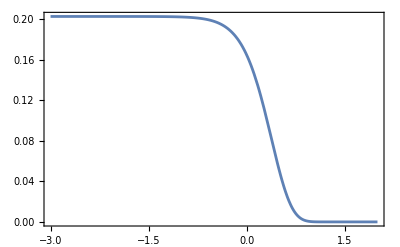

```mathematica
Plot[YMB[2,1,10^logx],{logx,-3,2}]
```

### Early time, small , high

At early time, the cross section behaves as , i.e.

```mathematica
l2
```

(x^2 y^4)/(384 π m_χ^2)

We can try to solve the Boltzmann equation directly. In this time regime, the behavior of the equilibrium is

```mathematica
YMB‵lowx=Series[YMB[g,m,x],{x,0,1}]//Normal
```

g/π^2

```mathematica
Ysol1[x_]=Y[x]/.DSolve[{Y'[x]==-Nν(mpl mχ l2)/(gH x^2)(Y[x]^2-(YMB‵lowx)^2),Y[0]==0},Y[x],x][[1]]//TrigToExp//Simplify
```

(g (ⅇ^((g m_pl N_ν x y^4)/(192 π^3 g_H m_χ))-1))/(π^2 (ⅇ^((g m_pl N_ν x y^4)/(192 π^3 g_H m_χ))+1))

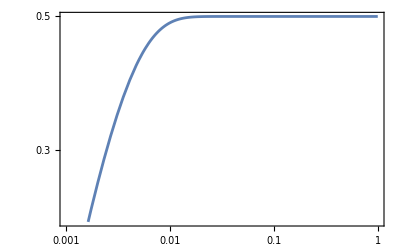

```mathematica
LogLogPlot[Ysol1[x]/(nν[g,mχ/x]/(mχ/x)^3+Ysol1[x])/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2},{x,10^-3,1}]
```

Another solution could be using the fact that the total number of χ and ν does not change. In this case, remember that the  in the equation is actually the neutrino density but we just approximated it as the equilibrium value. Replace it with , and use

N_ν Y_ν+Y_χ=Y_t
Y_ν=1/N_ν(Y_t-Y_χ)

Initially,  at some high temperature. Also remember that  does not change with time as long as the particle number does not change.

```mathematica
Ysol2[x_]=Y[x]/.DSolve[{Y'[x]==Nν(mpl mχ l2)/(gH x^2)((Yt-Y[x])^2/Nν^2-Y[x]^2),Y[0]==0},Y[x],x][[1]]//TrigToExp//Simplify
```

(Yt (ⅇ^((m_pl x y^4 Yt)/(192 π g_H m_χ))-1))/((N_ν+1) ⅇ^((m_pl x y^4 Yt)/(192 π g_H m_χ))+N_ν-1)

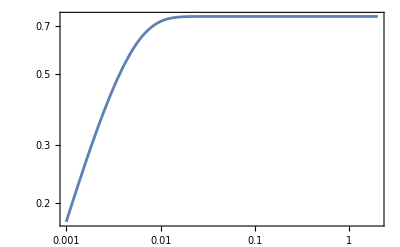

```mathematica
LogLogPlot[Ysol2[x]/Yν[2]/.Yt->(Nν nν[2,mχ*10^3])/((mχ*10^3)^3)/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2},{x,10^-3,2},PlotRange->Full]
```

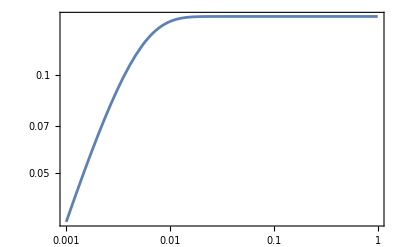

```mathematica
LogLogPlot[Ysol2[x]/.Yt->(Nν nν[2,mχ*10^3])/((mχ*10^3)^3)/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2},{x,10^-3,1}]
```

```mathematica
Ysol2[0.05]/.Yt->(Nν nν[2,mχ*10^3])/((mχ*10^3)^3)/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2}
```

0.151982

This solution is actually lower....Which one is correct?

Another question: where do we stop the plot?
Take the linear increasing part.

```mathematica
Ylin[g_,mχ_,y_,x_]=Y[x]/.DSolve[{Y'[x]==-Nν(mpl mχ l2)/(gH x^2)(-(YMB‵lowx)^2),Y[0]==0},Y[x],x][[1]]
```

(g^2 m_pl N_ν x y^4)/(384 π^5 g_H m_χ)

```mathematica
Ylin[g,mχ,y,mχ/T] T^3(*Subscript[n, χ]*)
```

(g^2 m_pl N_ν T^2 y^4)/(384 π^5 g_H)

This agrees with the previous result for the collision term solution.

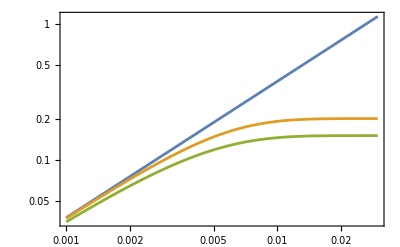

```mathematica
LogLogPlot[{Ylin[g,mχ,y,x]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2,Yt->(3 nν[2,mχ*10^3])/((mχ*10^3)^3)},Ysol1[x]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2,Yt->(3 nν[2,mχ*10^3])/((mχ*10^3)^3)},Ysol2[x]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2,Yt->(3 nν[2,mχ*10^3])/((mχ*10^3)^3)}},{x,10^-3,0.03},PlotStyle->{ColorData[97,1],ColorData[97,2],ColorData[97,3]}]
```

So actually the particle number conserved one gives lower result. We need full numerical solution to confirm which one is correct. (Of course, because the linear one is based on ‘keep the equilibrium value as a const’, so it has to agree with the solution 1)
The explanation is that the production should indeed be limited by the number of the source. So sol-2 should be correct. In this case, the equilibrium value should be . And we know that the initial value of Y_ν is a constant (g/π^2).

So we can just define

```mathematica
Yeq[g_,mχ_,x_]=3/4 YMB[g,mχ,x];
```

```mathematica
FindRoot[(Ysol2[x]/.Yt->(Nν nν[2,mχ*10^3])/((mχ*10^3)^3)/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2})==Yeq[2,1,x],{x,0.04}]
```

{x→0.0245741}

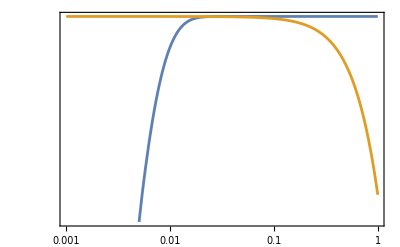

```mathematica
LogLogPlot[{Ysol2[x]/.Yt->(Nν nν[2,mχ*10^3])/((mχ*10^3)^3)/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,y->10^-5,mχ->10^-4,g->2},Yeq[2,1,x]},{x,0.001,1}]
```

The maximum value

```mathematica
ymax=Integrate[-Nν(mpl mχ σv[mχ,0,y,mχ/x])/(gH x^2)(-(YMB‵lowx)^2),{x,0,∞}]
Solve[ymax==Ylin[g,mχ,y,x],x][[1]]//Normal
```

(g^2 m_pl N_ν y^4)/(128 √3 π^5 g_H m_χ)

{x→√3}

Or if we use :

```mathematica
(x/.Solve[mχ/x==(Λ/.match),x][[1]]//Normal)/.{mϕ->0}
```

√3

This is too large actually, as we can see from the previous plot. The reason is apparent: if we are using Yeq at low x, which is a fixed number, and we only suppress the production until T at Λ, then we are talking about the case where the curve is already bent. Instead, we should go back to what we did in the collision term case

```mathematica
ymax=Integrate[(Nν mpl mχ  σvmol‵highT YMB[g,mχ,x]^2)/(gH x^2)//Simplify,{x,0,∞}]
```

(g^2 m_pl N_ν y^4)/(4096 π^3 g_H m_χ)

Note that in this case we still use the balanced value for the right-hand side, since to get the maximal value we are already assuming infinite neutrino source.

This immediately agrees.

```mathematica
xprod=x/.Solve[Ylin[g,mχ,y,x]==ymax,x][[1]]//Normal
```

(3 π^2)/32

```mathematica
Yprod[g_,mχ_,y_]=Ylin[g,mχ,y,xprod]
```

(g^2 m_pl N_ν y^4)/(4096 π^3 g_H m_χ)

If we want to make the trigger, we can use this to first judge whether this is freeze-in or freeze-out. If freeze-in, then just keep the analytical solved one until late time. If freeze-out, need to stop at a point where this solution reaches the equilibrium value, and then continue to the freeze-out solution.

### Late time, large , low

At late time, the equilibrium value drops, and the equation becomes

ⅆY/ⅆx=-λ/x^2 Y^2

```mathematica
yapprox[x_]=y[x]/.DSolve[{y'[x]==-λ/x^2 y[x]^2,y[∞]==Y∞},y[x],x][[1]]
```

(Y_∞ x)/(x-λ Y_∞)

The lower limit of x for this equation to make sense is simply

x=λ Y_∞

We define this to be x_f, where the DM freezes out. For a smaller x, the particle is in equilibrium. For large enough x, this approximated solution is justified. For some middle point, we need some trick to express between them. Determine it by

Y=(Y_∞x)/(a x+b)

```mathematica
Clear [a,b];
Ymiddle[x_]=(Y∞ x)/(a x+b)/.Solve[{Y∞ xf/(a xf+b)==Yf,Y∞ (2xf)/(2a xf+b)==(Y∞ 2 xf)/(2xf-λ Y∞)},{a,b}]/.{Y∞->xf/λ}//Simplify
```

{-(x_f Y_f x)/(x_f (λ Y_f-2 x_f)+x (x_f-λ Y_f))}

```mathematica
Collect[Denominator[Ymiddle[x]//Simplify]/(xf),x,Simplify]
```

{x (1-(λ Y_f)/x_f)-2 x_f+λ Y_f}

So the final result is

Y_mid=(Y_f x)/(x ((λ Y_f)/x_f-1)+x_f(2-λ Y_f/x_f))

In summary, we have

Y=(Y_∞ x)/(x-λ Y_∞), x>2 x_f
Y=Y_eq,x<x_f
Y=(Y_f x)/(x ((λ Y_f)/x_f-1)+x_f(2-λ Y_f/x_f)),x_f<x<2 x_f

The equilibrium value is nothing but the previously used one.

To calculate Y, the remaining question is the x_f.

```mathematica
λ[mχ_,mϕ_,y_]=Nν(mpl mχ)/gH σv0[mχ,mϕ,y];
xf[mχ_,mϕ_,y_]:=x/.FindRoot[x==Log[(λ[mχ,mϕ,y]/π^2)/(√x)]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},{x,20}]//Re
```

```mathematica
mχtest=10^-4;
mϕtest=10^-4;
ytest=10^-5;
xf[mχtest,mϕtest,ytest]
```

5.37277

```mathematica
Yfo[mχ_,mϕ_,y_,xfo_,x_]:=Piecewise[{{Yeq[g,mχ,x],x<=xfo},{(Yeq[g,mχ,xfo]*x)/(x((λ[mχ,mϕ,y]Yeq[g,mχ,xfo])/xfo-1)+xfo(2-(λ[mχ,mϕ,y]Yeq[g,mχ,xfo])/xfo)),xfo<x<=2xfo},{(x*xfo/λ[mχ,mϕ,y])/(x-xfo),x>2xfo}}]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV,g->2};
```

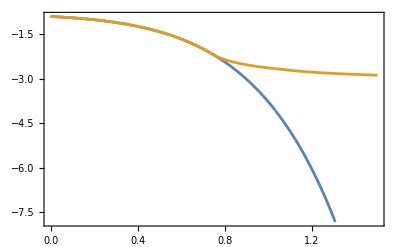

```mathematica
mχtest=10^-4;
mϕtest=10^-4;
ytest=10^-5;
Plot[{Log10[Yeq[2,mχtest,10^logx]],Log10[Yfo[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],10^logx]]},{logx,0,1.5}]
```

#### Numerical computation

```mathematica
SolveFreezeout[mχ_,mϕ_,y_,bd_]:=Block[{mpl,gH,Nν,s0,ρDM0,ρcrit,ΩDMhsq,sol,Yinf,inf,g},
gH=√((8 π^3)/90 3.91);
mpl=1.24*10^19*GeV;
Nν=3;
inf=1000;
g=2;
sol=lnY/.NDSolve[{ⅇ^lnY[x] lnY'[x]==(-λ[mχ,mϕ,y])/x^2(ⅇ^lnY[x]-Yeq[g,mχ,x])(ⅇ^lnY[x]+Yeq[g,mχ,x]),ⅇ^lnY[bd]==Yeq[g,mχ,bd]},lnY,{x,bd,inf}][[1]];
Yinf=(inf*ⅇ^sol[inf])/(inf+λ[mχ,mϕ,y]*ⅇ^sol[inf]);
s0=2891.2;
ρDM0=s0 mχ Yinf;
ρcrit=1.05*10^-5;
ΩDMhsq=ρDM0/ρcrit;
{sol,ΩDMhsq}
]
```

```mathematica
{sol,Ω}=SolveFreezeout[10^-4,10^-4,10^-5,0.01]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{InterpolatingFunction[…],29.7349}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{InterpolatingFunction[…],29.7349}

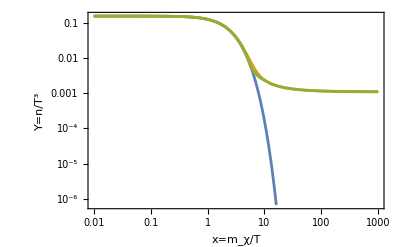

```mathematica
mχtest=10^-4;
mϕtest=10^-4;
ytest=10^-5;
{sol,Ω}=SolveFreezeout[mχtest,mϕtest,ytest,0.01]
LogLogPlot[{Yeq[2,mχtest,x]/.{gH->√(8 π^3/90 3.91),Nν->3,mpl->1.22*10^19*GeV},(ⅇ^sol[x]),Yfo[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],x]},{x,0.01,1000},FrameLabel->{"x=m_χ/T","Y=n/T^3"}]
```

So it agrees with the previous computation.

However, why the x is smaller than expected? The coupling is already large but we have x<20. If the coupling is smaller than the constraint for the ΔN_eff, i.e. y<10^-5, the x should be very small and DM density should be very large. This does not make sense.

## Combine all the periods

The first thing we need to discuss is whether the equilibrium is achieved.

```mathematica
Yfi[g_,mχ_,y_,x_]=Ysol2[x]/.Yt->Nν Yν[g]
```

(g N_ν (ⅇ^((g m_pl N_ν x y^4)/(192 π^3 g_H m_χ))-1))/(π^2 ((N_ν+1) ⅇ^((g m_pl N_ν x y^4)/(192 π^3 g_H m_χ))+N_ν-1))

```mathematica
Series[Yfi[g,mχ,y,x],{x,0,1}]//Normal
(Series[Yfi[g,mχ,y,x],{x,0,1}]//Normal)==Ylin[g,mχ,y,x]
```

(g^2 m_pl N_ν x y^4)/(384 π^5 g_H m_χ)

True

```mathematica
Y[mχ_,mϕ_,y_,xfo_,x_]:=Block[{xeq,gH,Nν,mpl,g},
gH=√(8 π^3/90 3.91);
Nν=3;
mpl=1.22*10^19*GeV;
g=2;
If[(Yprod[g,mχ,y]>Yeq[g,mχ,xprod]),
xeq=(10^lgx/.FindRoot[(Yfi[g,mχ,y,10^lgx]==Yeq[g,mχ,10^lgx]),{lgx,-2}]);Piecewise[{{Yfi[g,mχ,y,x],x<=xeq},{Yfo[mχ,mϕ,y,xfo,x],x>xeq}}],Piecewise[{{Yfi[g,mχ,y,x],x<=xprod},{Yfi[g,mχ,y,xprod],x>xprod}}]]];
```

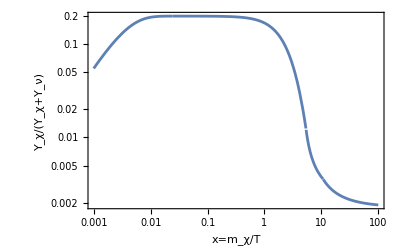

```mathematica
ytest=10^-5;
mχtest=10^-4;
mϕtest=10^-4;
theoryplot=LogLogPlot[Y[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],x]/(Y[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],x]+3Yν[2]),
{x,0.001,100},FrameLabel->{"x=m_χ/T","Y_χ/(Y_χ+Y_ν)"}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

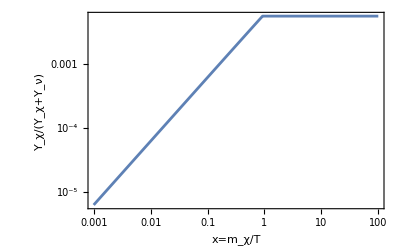

```mathematica
ytest=10^-6;
mχtest=10^-4;
mϕtest=10^-4;
theoryplot=LogLogPlot[Y[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],x]/(Y[mχtest,mϕtest,ytest,xf[mχtest,mϕtest,ytest],x]+3Yν[2]),
{x,0.001,100},FrameLabel->{"x=m_χ/T","Y_χ/(Y_χ+Y_ν)"}]
```